FittedModel[-0.288195+0.0000292202 x^2]

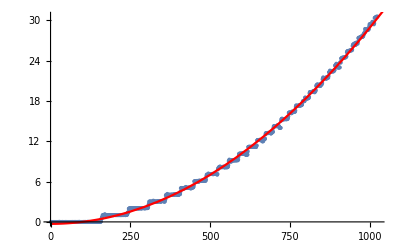

0.99956

{6.5132×10^-86,2.78370505147×10^-1544}

```mathematica
SetOptions[EvaluationNotebook[],CellContext->Notebook]
name := "unionp-i"
data :=Import[StringJoin["/Users/greg/Documents/School/Science_Research/workspace/ODRA-with-Enums/greg/queries/benchmarks-",name,".csv"], "Table", {"FieldSeparators" -> ";"}][[All,{1,3}]]
nlm = NonlinearModelFit[data, a+c*x^2,{a,c},x]
Show[ListPlot[data],Plot[nlm[x],{x,0,2048},PlotStyle->Red]]
nlm["RSquared"]
nlm["ParameterPValues"]
```